```mathematica
ClearSystemCache[];
ClearAll["Global`*"];
```

### Task & Variables

Waist of an ideal gaussian beam (waist = 10um, wavelength = 1.55um) is placed at a double focal distance from an ideal aberration-free lens with focal length = 1.5mm. A rigid diaphragm of variable diameter is placed directly behind the lens coaxially with the system’s optical axis. Find relation between diaphragm radius and beam parameter product M^2. Beam size can be found via method of second moments.

```mathematica
w0 = (10×10^-6);
λ=1.55×10^-6;
F = 1.5×10^-3;
X = 1000×10^-6;
Y = 1000×10^-6;
k0=(2π)/λ;
```

### Calculation

#### Mesh (Cartesian coordinates and spatial frequencies)

```mathematica
n=2^9;
xmesh=Range[-X/2,X/2,X/n];
ymesh=Range[-Y/2,Y/2,Y/n];
rkxmesh = ((2π×Range[-n/2,n/2,1.0])/X);
rkymesh = ((2π×Range[-n/2,n/2,1.0])/Y);
kxpos=Take[rkxmesh,{n/2+1,n+1}];
kxneg=Take[rkxmesh,{-(n+1),n/2}];
kxmesh=Join[kxpos,kxneg];
kypos=Take[rkymesh,{n/2+1,n+1}];
kyneg=Take[rkymesh,{-(n+1),n/2}];
kymesh=Join[kypos,kyneg];
```

#### Propagation equation & optical elements

(∂φ(x,y,z))/(∂z)=-i/(2 β_0)(∇_xy)^2φ(x,y,z) (no focusing in free propagation)
Free propagation solution (β_0= n×k_0, index of refraction n = 1): φ̃(z)=e^((-i(k_x^2+k_y^2)dz)/(2 k_0))= e^((-i×k_s^2×dz)/(2 k_0))
Gaussian beam at waist: A(x,y)~e^(-(x^2+y^2)/w_0^2)
Lens operator: D_lens = e^(-iπ/λF(x^2+y^2))
Diaphragm : x^2 + y^2 ≤ d^2

```mathematica
GaussianBeam[x_,y_,w_]:=GaussianBeam[x,y,w]=N[Exp[-(x^2+y^2)/w^2]];
```

```mathematica
Beam= ParallelTable[GaussianBeam[x,y,w0],{x,-X/2,X/2,X/n},{y,-Y/2,Y/2,Y/n}];
```

General::munfl: Exp[-3381.35] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3361.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3342.44] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2881.47] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3105.62] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2861.98] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3086.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2842.56] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3066.71] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2518.46] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2498.97] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2479.55] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2534.33] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2514.84] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2756.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2936.74] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2495.42] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2737.01] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2917.25] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3164.67] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2717.59] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2897.83] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3145.18] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3125.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3440.28] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3420.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3763.58] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4134.56] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3401.37] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3744.09] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4115.07] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3724.67] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4095.65] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
ExkMat[d_]:=ExkMat[d]=Module[{tab},tab=Table[0.0,{i,n+1},{j,n+1}];For[i=1,i≤n+1,i++,For[j=1,j≤n+1,j++,tab[[i,j]]=N[Exp[-I/(2k0)×((kxmesh[[i]])^2+(kymesh[[j]])^2)×d]]]];tab];
```

#### Free propagation

```mathematica
FreePropagation[beam_,d_]:=FreePropagation[beam,d]=Block[{FftBeam,changeRows,FftBeamShift,prop,propChangeRows,propShift,final},FftBeam=Fourier[beam,FourierParameters->{1, -1}];
prop=FftBeam×ExkMat[d];

final=Evaluate[InverseFourier[prop,FourierParameters->{1, -1}]];final];
```

```mathematica
beforeLens[d_]:=beforeLens[d]=FreePropagation[Beam,d];
```

#### Let’s compare the result to known formula for Gaussian beam propagation

```mathematica
Zr=(π×w0^2)/λ;
w[d_]:=w[d]=w0×√(1+(d/Zr)^2);
gaussProp[d_,x_,y_]:=gaussProp[d,x,y]=w0/w[d]×GaussianBeam[x,y,w0];
```

```mathematica
{FindMaximum[gaussProp[2F,x,0],{x,0}],Max[Abs[FreePropagation[Beam,2F][[All,n/2+1]]]]}
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{{0.0674075,{x→0.}},0.0671461}

#### Lens

```mathematica
Lens[x_,y_]:=Lens[x,y]=Exp[-(I×π)/(λ×F)(x^2+y^2)];
LensMat=ParallelTable[N[Lens[x,y]],{x,-X/2,X/2,X/n},{y,-Y/2,Y/2,Y/n}];
afterLens[d_]:=afterLens[d]=beforeLens[d]×LensMat;
```

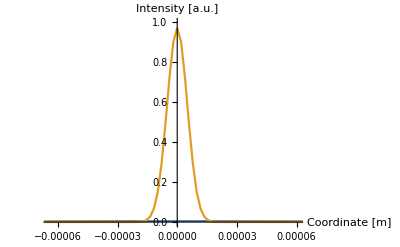

```mathematica
ListLinePlot[{Transpose[{xmesh,Abs[FreePropagation[afterLens[2F],0][[All,n/2+1]]]^2}],Transpose[{xmesh,Abs[FreePropagation[afterLens[2F],2F][[All,n/2+1]]]^2}]},PlotRange->{{xmesh[[7n/16]],xmesh[[9n/16]]},{0,1}},AxesLabel->{"Coordinate [m]","Intensity [a.u.]"}]
```

#### Diaphragm

```mathematica
Diaphragm=Evaluate[Piecewise[{{1.0,x^2+y^2<d^2}},0.0]];
DiaMat[diam_]:=DiaMat[diam]=ParallelTable[N[Chop[Diaphragm/.{x->xx,y->yy,d->diam}]],{xx,-X/2,X/2,X/n},{yy,-Y/2,Y/2,Y/n}];
```

```mathematica
afterDiaphragm[d_,diam_]:=afterDiaphragm[d,diam]=afterLens[d]×DiaMat[diam];
```

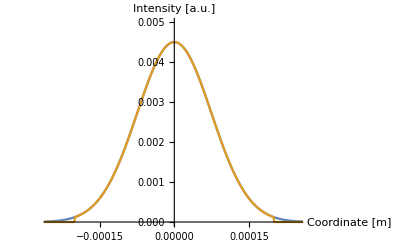

```mathematica
ListLinePlot[{Transpose[{xmesh,Abs[afterLens[2F][[All,n/2+1]]]^2}],Transpose[{xmesh,Abs[afterDiaphragm[2F,2×10^-4][[All,n/2+1]]]^2}]},PlotRange->{{xmesh[[n/4]],xmesh[[3n/4]]},{0,0.005}},AxesLabel->{"Coordinate [m]","Intensity [a.u.]"}]
```

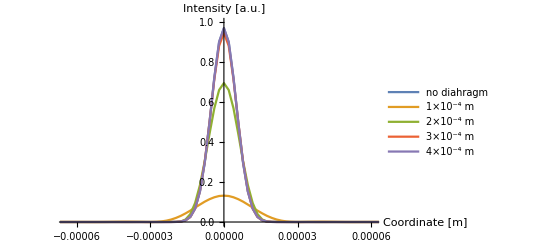

```mathematica
ListLinePlot[{Transpose[{xmesh,Abs[FreePropagation[afterLens[2F],2F][[All,n/2+1]]]^2}],Transpose[{xmesh,Abs[FreePropagation[afterDiaphragm[2F,1×10^-4],2F][[All,n/2+1]]]^2}],Transpose[{xmesh,Abs[FreePropagation[afterDiaphragm[2F,2×10^-4],2F][[All,n/2+1]]]^2}],Transpose[{xmesh,Abs[FreePropagation[afterDiaphragm[2F,3×10^-4],2F][[All,n/2+1]]]^2}],Transpose[{xmesh,Abs[FreePropagation[afterDiaphragm[2F,4×10^-4],2F][[All,n/2+1]]]^2}]},PlotRange->{{xmesh[[7n/16]],xmesh[[9n/16]]},{0,1}},ImageSize->Full,AxesLabel->{"Coordinate [m]","Intensity [a.u.]"},PlotLegends->{"no diahragm","1×10^-4 m","2×10^-4 m","3×10^-4 m","4×10^-4 m"}]
```

#### Calculation of M2 factors

Using ratio of effective mode areas A_eff at Z = 0 and Z = 2F (after exiting lens): A_eff= ((∫|E|^2 dA)^2)/(∫|E|^4 dA)

```mathematica
ClearAll[Aeff];
Aeff[beam_]:=Aeff[beam]=((Sum[Sum[Abs[beam[[i,j]]]^2×(xmesh[[2]]-xmesh[[1]])×(ymesh[[2]]-ymesh[[1]]),{j,3n/8,5n/8}],{i,3n/8,5n/8}])^2)/Sum[Sum[Abs[beam[[i,j]]]^4×(xmesh[[2]]-xmesh[[1]])×(ymesh[[2]]-ymesh[[1]]),{j,3n/8,5n/8}],{i,3n/8,5n/8}];
```

Check if Aeff of initial beam is equal to πw^2

```mathematica
{Aeff[Beam],N[π×w0^2]}
```

General::munfl: (1.0202×10^-140)^4 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.39904×10^-138)^4 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.77763×10^-136)^4 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{3.14159×10^-10,3.14159×10^-10}

```mathematica
ClearAll[θ,θGauss, M2new,M2newtable];
```

```mathematica
ratio[beam_]:=ratio[beam]=(Aeff[beam]/π)/(Aeff[FreePropagation[beam,2F]]/π);
ratioGauss=(Aeff[afterLens[2F]]/π)/(Aeff[FreePropagation[afterLens[2F],2F]]/π);
M2[beam_]:=M2[beam]=ratioGauss/ratio[beam];
```

```mathematica
ratio1[beam_]:=ratio1[beam]=(√(Aeff[beam]/π))/(√(Aeff[FreePropagation[beam,2F]]/π));
ratioGauss1=(√(Aeff[afterLens[2F]]/π))/(√(Aeff[FreePropagation[afterLens[2F],2F]]/π));
M21[beam_]:=M21[beam]=ratioGauss1/ratio1[beam];
```

```mathematica
θGauss=λ/(π×√(Aeff[afterLens[2F]]/π));
θ[beam_]:=θ[beam]=(√(Aeff[beam]/π))/(2F);
M2new[beam_]:=M2new[beam]=(θ[beam]×√(Aeff[beam]/π))/(λ/π);
M2New[beam_]:=M2New[beam]=(√(Aeff[beam]/π))/(√(Aeff[FreePropagation[beam,2F]]/π));
```

```mathematica
DiaphragmTable=Table[i,{i,1×10^-4,5×10^-4,0.25×10^-4}];
M2table=Table[0.0,{i,Length[DiaphragmTable]},{j,2}];
For[i=1,i≤Length[DiaphragmTable],i++,M2table[[i,1]]=DiaphragmTable[[i]];M2table[[i,2]]=M2[afterDiaphragm[2F,DiaphragmTable[[i]]]]];
```

```mathematica
θ[afterDiaphragm[2F,0.002]]
```

0.0417391

```mathematica
M2newtable=Table[0.0,{i,Length[DiaphragmTable]},{j,2}];
For[i=1,i≤Length[DiaphragmTable],i++,M2newtable[[i,1]]=DiaphragmTable[[i]];M2newtable[[i,2]]=M2new[afterDiaphragm[2F,DiaphragmTable[[i]]]]];
```

```mathematica
M2Newtable=Table[0.0,{i,Length[DiaphragmTable]},{j,2}];
For[i=1,i≤Length[DiaphragmTable],i++,M2Newtable[[i,1]]=DiaphragmTable[[i]];M2Newtable[[i,2]]=M2New[afterDiaphragm[2F,DiaphragmTable[[i]]]]];
```

```mathematica
M21table=Table[0.0,{i,Length[DiaphragmTable]},{j,2}];
For[i=1,i≤Length[DiaphragmTable],i++,M21table[[i,1]]=DiaphragmTable[[i]];M21table[[i,2]]=M21[afterDiaphragm[2F,DiaphragmTable[[i]]]]];
```

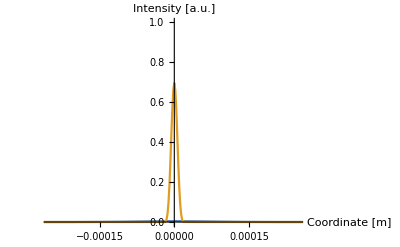

```mathematica
ListLinePlot[{Transpose[{xmesh,Abs[afterDiaphragm[2F,2×10^-4][[All,n/2+1]]]^2}],Transpose[{xmesh,Abs[FreePropagation[afterDiaphragm[2F,2×10^-4],2F][[All,n/2+1]]]^2}]},PlotRange->{{xmesh[[n/4]],xmesh[[3n/4]]},{0,1}},AxesLabel->{"Coordinate [m]","Intensity [a.u.]"}]
```

```mathematica
θGauss
```

0.00394019

```mathematica
θ[afterDiaphragm[2F,0.0005]]
```

0.0417391

```mathematica
Aeff[afterDiaphragm[2F,0.0005]]
```

4.92582×10^-8

```mathematica
{M2table//MatrixForm,M21table//MatrixForm}
```

{(0.0001 | 7.11777
0.000125 | 3.23788
0.00015 | 2.03545
0.000175 | 1.54749
0.0002 | 1.29477
0.000225 | 1.15082
0.00025 | 1.0723
0.000275 | 1.03176
0.0003 | 1.01262
0.000325 | 1.00452
0.00035 | 1.00144
0.000375 | 1.0004
0.0004 | 1.00009
0.000425 | 1.00002
0.00045 | 1.
0.000475 | 1.
0.0005 | 1.),(0.0001 | 2.66792
0.000125 | 1.79941
0.00015 | 1.42669
0.000175 | 1.24398
0.0002 | 1.13788
0.000225 | 1.07276
0.00025 | 1.03552
0.000275 | 1.01576
0.0003 | 1.00629
0.000325 | 1.00226
0.00035 | 1.00072
0.000375 | 1.0002
0.0004 | 1.00005
0.000425 | 1.00001
0.00045 | 1.
0.000475 | 1.
0.0005 | 1.)}

### Results

#### Beam quality factor M2 vs diaphragm diameter

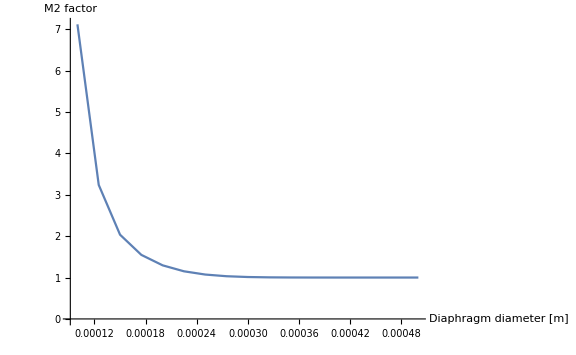

```mathematica
ListLinePlot[M2table,PlotRange->All,AxesLabel->{"Diaphragm diameter [m]","M2 factor"},ImageSize->Large]
```

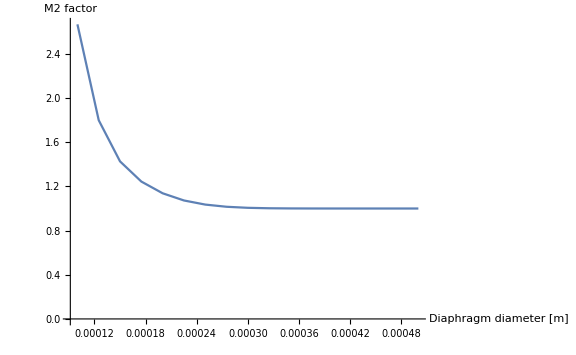

```mathematica
ListLinePlot[M21table,PlotRange->All,AxesLabel->{"Diaphragm diameter [m]","M2 factor"},ImageSize->Large]
```